{x→-0.707107 √(r-1. √(4.+r^2)),x→0.707107 √(r-1. √(4.+r^2)),x→-0.707107 √(r+√(4.+r^2)),x→0.707107 √(r+√(4.+r^2))}

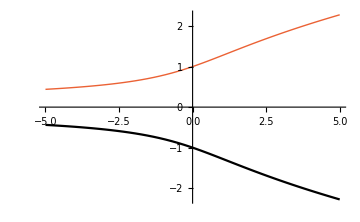

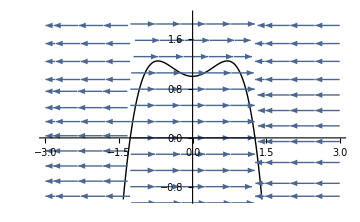

```mathematica
Clear[f,r,x,λ,rval]
f=r x^2 - x^4+λ;
λ=1.;
roots=Solve[f==0,x]//Flatten
Plot[{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]],roots[[4]][[2]]},{r,-5,5},ImageSize->Medium]
rval=1.;
Show[Plot[f/.r->rval,{x,-3,3},ImageSize->Medium,PlotRange->{All,{-1,2}}],
StreamPlot[{f/.r->rval,0},{x,-3,3},{y,-2,2},ImageSize->Medium]]
```